# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_]:=Exp[x+3]/(100 x+2)
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
domain=Complement[Reals,{-1/50}]
```

Complement::normal: Nonatomic expression expected at position 1 in Complement[,{-1/50}].

Complement[ℝ,{-1/50}]

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
limitLeft=Limit[f[x],x->-1/50,Direction->-1]
limitRight=Limit[f[x],x->-1/50,Direction->1]
limitNegInf=Limit[f[x],x->-Infinity]
limitPosInf=Limit[f[x],x->Infinity]
```

∞

-∞

0

∞

d. Izračunajte odvod funkcije .

```mathematica
D[f[x],x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
kritičneTočke=Solve[D[f[x],x]==0,x];
lokalniEkstrem=Table[{x,f[x]}/. cp,{cp,kritičneTočke}]
```

{{49/50,ⅇ^(199/50)/100}}

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
df=D[f[x],x];
narašča=Reduce[df>0&&x∈Reals,x]
pada=Reduce[df<0&&x∈Reals,x]
```

x>49/50

x<-1/50||-1/50<x<49/50

g. Narišite graf funkcije  na intervalu [-5, 5].

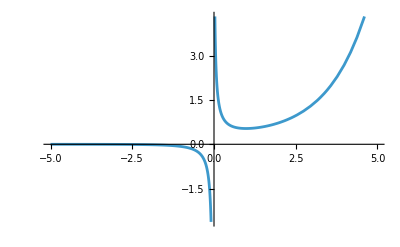

```mathematica
Plot[f[x],{x,-5,5}]
```

h. Določite zalogo vrednosti funkcije .

```mathematica
minVrednost=f[49/50];
zalogaVrednosti={Interval[{-Infinity,0}],Interval[{minVrednost,Infinity}]}
```

{Interval[{-∞,0}],Interval[{ⅇ^(199/50)/100,∞}]}

i. Izračunajte nedoločeni integral funkcije .

```mathematica
nedIntegral=Integrate[f[x],x]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
volumen=N[Pi*Integrate[f[x]^2,{x,0.5,2}],10];
```

```mathematica
zaokroženo=NumberForm[volumen,{Infinity,3}]

RevolutionPlot3D[f[x],{x,0.5,2},PlotStyle->Opacity[0.5]]
```

1.665

-Graphics3D-

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll["Global`*"]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
g[x_]:=(1+x^(2.1))/(3+x);
vrednosti=Table[{i,g[i]},{i,1,100}]
```

{{1,0.5},{2,1.05742},{3,1.84085},{4,2.76845},{5,3.79568},{6,4.89604},{7,6.05259},{8,7.25393},{9,8.49202},{10,9.76096},{11,11.0563},{12,12.3747},{13,13.7134},{14,15.0702},{15,16.4433},{16,17.8313},{17,19.2328},{18,20.6469},{19,22.0727},{20,23.5093},{21,24.956},{22,26.4123},{23,27.8776},{24,29.3514},{25,30.8333},{26,32.3228},{27,33.8198},{28,35.3238},{29,36.8345},{30,38.3516},{31,39.875},{32,41.4044},{33,42.9396},{34,44.4803},{35,46.0265},{36,47.5778},{37,49.1343},{38,50.6956},{39,52.2618},{40,53.8326},{41,55.4079},{42,56.9876},{43,58.5716},{44,60.1598},{45,61.7521},{46,63.3483},{47,64.9485},{48,66.5525},{49,68.1602},{50,69.7716},{51,71.3865},{52,73.005},{53,74.6269},{54,76.2521},{55,77.8807},{56,79.5125},{57,81.1475},{58,82.7856},{59,84.4268},{60,86.0711},{61,87.7183},{62,89.3684},{63,91.0214},{64,92.6772},{65,94.3359},{66,95.9972},{67,97.6613},{68,99.3281},{69,100.997},{70,102.669},{71,104.344},{72,106.021},{73,107.7},{74,109.382},{75,111.067},{76,112.754},{77,114.443},{78,116.134},{79,117.828},{80,119.524},{81,121.222},{82,122.923},{83,124.625},{84,126.33},{85,128.037},{86,129.746},{87,131.457},{88,133.171},{89,134.886},{90,136.603},{91,138.322},{92,140.044},{93,141.767},{94,143.492},{95,145.219},{96,146.948},{97,148.679},{98,150.412},{99,152.146},{100,153.883}}

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
g[x_]:=(1+x^(2.1))/(3+x);
izbrani=Select[vrednosti,PrimeQ[Mod[#[[1]],10]]&]
```

{{2,1.05742},{3,1.84085},{5,3.79568},{7,6.05259},{12,12.3747},{13,13.7134},{15,16.4433},{17,19.2328},{22,26.4123},{23,27.8776},{25,30.8333},{27,33.8198},{32,41.4044},{33,42.9396},{35,46.0265},{37,49.1343},{42,56.9876},{43,58.5716},{45,61.7521},{47,64.9485},{52,73.005},{53,74.6269},{55,77.8807},{57,81.1475},{62,89.3684},{63,91.0214},{65,94.3359},{67,97.6613},{72,106.021},{73,107.7},{75,111.067},{77,114.443},{82,122.923},{83,124.625},{85,128.037},{87,131.457},{92,140.044},{93,141.767},{95,145.219},{97,148.679}}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
anonF=(#^2+1)&;
izbraniNova=Map[Append[#,anonF[#[[1]]]]&,izbrani]
```

{{2,1.05742,5},{3,1.84085,10},{5,3.79568,26},{7,6.05259,50},{12,12.3747,145},{13,13.7134,170},{15,16.4433,226},{17,19.2328,290},{22,26.4123,485},{23,27.8776,530},{25,30.8333,626},{27,33.8198,730},{32,41.4044,1025},{33,42.9396,1090},{35,46.0265,1226},{37,49.1343,1370},{42,56.9876,1765},{43,58.5716,1850},{45,61.7521,2026},{47,64.9485,2210},{52,73.005,2705},{53,74.6269,2810},{55,77.8807,3026},{57,81.1475,3250},{62,89.3684,3845},{63,91.0214,3970},{65,94.3359,4226},{67,97.6613,4490},{72,106.021,5185},{73,107.7,5330},{75,111.067,5626},{77,114.443,5930},{82,122.923,6725},{83,124.625,6890},{85,128.037,7226},{87,131.457,7570},{92,140.044,8465},{93,141.767,8650},{95,145.219,9026},{97,148.679,9410}}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
zaokroženSeznam=Map[Floor,izbraniNova,{2}];
deljivaS3=Select[Flatten[zaokroženSeznam],Divisible[#,3]&];
vsota=Total[deljivaS3]
```

1224

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

```mathematica
pravilo=x->y+1;
```

x→1+y

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

```mathematica
izrazNov=izraz/. pravilo;
vrednost=izrazNov/. y->1
```

9

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

```mathematica
f[x_]:=x^5-4 x^3+x^2+3 x-2;
prepis=x^n_.:>2*n*x^(n-1);
fNova=f[x]/. prepis
```

4+4 x-24 x^2+10 x^4

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
ClearAll[g,prepis];
g[x_]:=x^2025;
prepis=x^n_.:>2*n*x^(n-1);
rezultat=g[x]//.prepis
```

50398368281427932218648879435231938463740385018981535698812268015338181004233440447381646866294649137295770736080469736945451611684750816765429554471637334740001501598594534331032597748870114113252783072166682814172068709911917364527670863883520516109439601156193945874792418928290668384483145069678513417023938105197860144611773205279706766202805843264139448746199305215127720321701276709845616174477309942850203548438040089622336966153411830490817057562106931531373918440170427190651651291509552173028816653090880390410124613848728073011328868123141697924655871826331444579308611777280419850267069252673270871011426254357267368088452082465883184239579711876955098766888944012424902202472271117002294137662187289730800759111802372042140653613067252559731522689247380713145492578337815032419350558968864802128461806874559617521283051370755651707740483512222942706896220294417736193587422327122493937349053869975080905613341074409856370591228384540547462914934749674719967407166802461771705251988344039091673676298116243611776342480035262913603551206042071315087318298326889285219375078455982381393454535577721929438654313965821718383901579698734794350250889663135600060267632497272846914533248842500900713634107682071942771037059022312127330963916685751533986947045469104263841764085580318979418735565253845707799988662933280173998514215705184510761817648057020681176818220390110689656625808227512142676841258136175561410947541782146102351895347529940329984914134433740808349191681475086917263487402878055232197270993711545771847556111711281997483248420166055210353392934125948685460566822744786039576242387862908516817224599299713349060264891959350554223061569168669110591805940730151727692199083879400823117583782198980698228264952578676889423145009014136180598583831203143150100531144951255305106993279376557370971110685989855895030198617612041846902095867360527064745793077830079135789964591216542266512678813389164497010888450351041236032639088105974609564631099061310599209708371314250526770701710766626107045861787653889003611576409779172464463242707894305376709109642696047509122280055304451115974848420434860156383305962037671954406699655583994795663510601684854237579949676905335113632193064955399389561385744162857819426512767368172765500287185437261645580498135256227942357992233322328859144428344042288725951437817517837464519950437220064136500309507342762578998726422425089837109813055298284976874391723486248221223852607287265397559132595663209783775671975584023422987152768103558329994900247856991510475806100353129547949644060691118916193071914434850692466626683729439853214096339146500243578585257487063051166303039907706415429444803927878750137338266134472773973221472727600949383766106911149634903145266656154915801797612851822101502116797815473067867242247111494164207900579844107703747362187983792806078894693046928886492253793747369477804531754619810737589232942522626385421524638325524024005207820152399363798472344877252389041739723799926442360281798478754277012460923763822491378775442951057966458509377088731192314746431220438947715095621666217601413918543497280977670633747283389886312690158746807940383892702560403217898461005293765397242276719952496820297356405521740190148603296550761503263202284898483307542237932896389095439598745469468063384800981068259953253669057691618851616849675218141468056032841020120124680808128865645517409556038778192444230766517032247554159406211941137968151583011432328046188251111236948498802384774974647508492683293118778961020239136214064956581249828243944208247680407453854634884375433188372353767648773719463340088881082049941589797645059094777824814347927203117365919295367343912642360223907512262369369855838269001900283480240046030415074041883232641405454751307931164835059639251472625956849249357796888050345761694968082204672316345803171760233329560309880471746128202450573837707088603916206020060867328649052538141408261875447873829253175222016646942255218521984469687729585300504283876657214908545122007504505712733546938734232268373353216685193178358011406753089626267197383969407628287524144077822016277383051577009874398005197088665479092679271313594991166607754104348072869807371546305492194633288585969920541760234924234398716156188222734587067016581457508357217265884571170660526794251877640591785974681599769207800403278248496157497691759412755492660679009688014436337345914718972271116999146535015610707610676807866786091272732780062722177003533267392305513905793304800537113795041182031324839883344098203572618875925136662287882826258150143936751296015910445315203133784438388287551424056364616010530628335291868026133228520882011677504896916049976484427353704513206411115070053176842648573953894522165919567029218691394530481648877691448341432146369465338011628835910998889792276758626808532127715478714083278369975889399889416435758457766160915652102935080511752686994145413121791529150371942818032220064420438312771296052695348216049200144764623907049092310297935611369721715215899981986337735370707564487754916502416900076363615082283021894883085394674555526115761223196599572125751561873861912413123623481175538653100059793009154858030691295761299059755675628952479096178480559054665435398504142231434277732945554578761101867219153240449436496974399016155008861275625502155124801551042999516450753098558854479776240953367603643648905146985196295677193844605532089806208809319138340271573956209264727151370742533566263485843394947797489652941301882536037445133724566968842953387012443292641274505072025767819927770557516039669566906323547250244633448367870181579609366206792796631254793079428217242677923356677567603009614313287894711849918301221030984061176855166678119310424558895084058482575915998896906670458144240888397176889456888673162594021398810194225173064220040384348590755559698185143754027548354193622244267987775105811077092684149925836157878779338206740900883049661599937122030108872466708392741885421324072381906671370240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
fibPravila={Fib[0]->0,Fib[1]->1,Fib[n_Integer/;n>=2]:>Fib[n-1]+Fib[n-2]};
rezultat=Fib[10]//.fibPravila
```

55